## 1) Set base form viscous SD dynamical system (precomputed

### SD Mℛ^0 equivalence

```mathematica
Mℛ0equivSK[νn_,wn_[t_],Ln_[t_],Hn_[t_]]=ⅇ (wn[t] Hn'[t]-(Ln[t]^2 wn[t] Hn'[t])/(4 Hn[t]^2)+(Ln[t] wn[t] Ln'[t])/(2 Hn[t])+Hn[t] wn'[t]+(Ln[t]^2 wn'[t])/(4 Hn[t]))==(ⅇ νn (-8 Hn[t]^2-(32 Hn[t]^4)/Ln[t]^2+3 Ln[t]^2) wn[t])/(4 Hn[t]^3);
```

### SD Mz^1 equivalence

```mathematica
Mz1equivSK[νn_,wn_[t_],Ln_[t_],Hn_[t_]]=4 ⅇ Hn[t] wn[t] Hn'[t]+2 ⅇ Hn[t]^2 wn'[t]==(ⅇ νn (-32 Hn[t]^4+Ln[t]^4) wn[t])/(2 Hn[t]^2 Ln[t]^2)+(ⅇ^2 (8 Hn[t]^2+Ln[t]^2) wn[t]^2)/(64 Hn[t]);
```

### SD Mℛ^2 equivalence

```mathematica
Mℛ2equivSK[νn_,wn_[t_],Ln_[t_],Hn_[t_]]=-(ⅇ Ln[t]^4 wn[t] Hn'[t])/(4 Hn[t]^2)+(ⅇ Ln[t]^3 wn[t] Ln'[t])/Hn[t]+(ⅇ Ln[t]^4 wn'[t])/(4 Hn[t])==(3 ⅇ νn Ln[t]^4 wn[t])/(4 Hn[t]^3)-(ⅇ^2 Ln[t]^4 wn[t]^2)/(32 Hn[t]^2);
```

## 2) Define numeric interval

### t initial

```mathematica
tInitial=0;
```

### t final

```mathematica
tFinal=3*3600;
```

# 3) Solve Viscous SD dynamical system

## Clear previous system

```mathematica
ClearAll[SKDynamicSystemSolve]
```

## Set explicit SD parameter tendencies

```mathematica
SKDynamicSystemSolve=ParametricNDSolve[{Mℛ0equivSK[νn,wn[t],Ln[t],Hn[t]],Mz1equivSK[νn,wn[t],Ln[t],Hn[t]],Mℛ2equivSK[νn,wn[t],Ln[t],Hn[t]],wn[0]==wnInitial,Ln[0]==LnInitial,Hn[0]==HnInitial},{wn,Ln,Hn},{t,tInitial,tFinal},{νn,wnInitial,LnInitial,HnInitial}]
```

{wn→ParametricFunction[<>],Ln→ParametricFunction[<>],Hn→ParametricFunction[<>]}

# 4) Set explicit SD parameter tendencies

### wn tendency - ((ẇ)_n)

```mathematica
wnNumericSolveSK[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=wn[νn,wnInitial,LnInitial,HnInitial][t]/.SKDynamicSystemSolve;
```

### Ln tendency - ((L̇)_n)

```mathematica
LnNumericSolveSK[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=Ln[νn,wnInitial,LnInitial,HnInitial][t]/.SKDynamicSystemSolve;
```

### Hn tendency - ((Ḣ)_n)

```mathematica
HnNumericSolveSK[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=Hn[νn,wnInitial,LnInitial,HnInitial][t]/.SKDynamicSystemSolve;
```

# 5) Define the implicit SD (also part of the DK) parameters

### αn - (α_n)

```mathematica
αnDef[Ln_,Hn_]=Ln/Hn;
```

### Rn - (R_n)

```mathematica
RnDef[νn_,wn_,Hn_]=(ⅇ*wn*Hn)/νn;
```

### τn - (τ_n)

```mathematica
τnDef[wn_,Hn_]=Hn/wn;
```

# 6) Set the implicit SK parameter tendencies

### αn tendency ((α̇)_n)

```mathematica
DαSK[τn_,αn_,Rn_]=-(ⅇ αn (64+20 αn^2+αn^4))/(128 (8+3 αn^2) τn)+(64 ⅇ+40 ⅇ αn^2+8 ⅇ αn^4-ⅇ αn^6)/(Rn (32 αn τn+12 αn^3 τn));
```

### Rn tendency ((Ṙ)_n)

```mathematica
DRSK[τn_,αn_,Rn_]=(ⅇ Rn αn^2 (16+αn^2))/(64 (8+3 αn^2) τn)+(ⅇ (-128-64 αn^2+6 αn^4+αn^6))/(2 αn^2 (8+3 αn^2) τn);
```

### τn tendency ((τ̇)_n)

```mathematica
DτSK[αn_,Rn_]=-(ⅇ (-4+αn^2))/(4 (8+3 αn^2))+(ⅇ (64+48 αn^2-5 αn^4))/(Rn αn^2 (8+3 αn^2));
```

# 7) Define numeric tendencies for SK implicit parameters

### αn tendency ((α̇)_n)

```mathematica
DαnSKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=αnDef[LnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial],HnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial]];
```

### Rn tendency ((Ṙ)_n)

```mathematica
DRnSKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=RnDef[νn,wnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial],HnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial]];
```

### τn tendency ((τ̇)_n)

```mathematica
DτnSKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=τnDef[wnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial],HnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial]];
```

# 8) Define the implicit quantities of interest for SK

### σn - (σ_n)

```mathematica
σnDef[wn_,Ln_]=(Ln^2*π* wn)/ⅇ;
```

### Γn - (Γ_n)

```mathematica
ΓnDef[wn_,Ln_,Hn_]=ⅇ*wn*Hn*(Ln^2/(4*Hn^2)+1);
```

# 9) Set the implicit SK quantities of interest from numeric integrate

### σn (σ_n)

```mathematica
DσnSKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=σnDef[wnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial],LnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial]];
```

### Γn (Γ_n)

```mathematica
DΓnSKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_]=ΓnDef[wnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial],LnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial],HnNumericSolveSK[t,νn,wnInitial,LnInitial,HnInitial]];
```

# 10) Generate SK Phase Space

## Generate the time implicit phase plane

```mathematica
PhasePlaneSK[Type_,PlotSize_,LabelSize_]:=StreamPlot[{DαSK[1,αn,Rn],DRSK[1,αn,Rn]},{αn,.1,10},{Rn,1,1000000},ScalingFunctions->{"Log10","Log10"},PlotLegends->Automatic,Frame->True,FrameTicks->{{{{10^0,"0"},{10^1,"1"},{10^2,"2"},{10^3,"3"},{10^4,"4"},{10^5,"5"},{10^6,"6"}},{{10^0,"0"},{10^1,"1"},{10^2,"2"},{10^3,"3"},{10^4,"4"},{10^5,"5"},{10^6,"6"}}},{{{10^-1,"-1"},{10^(-.8),"-.8"},{10^(-.6),"-.6"},{10^(-.4),"-.4"},{10^(-.2),"-.2"},{10^0,"0"},{10^(.2),".2"},{10^(.4),".4"},{10^(.6),".6"},{10^(.8),".8"},{10^1,"1"}},{{10^-1,"-1"},{10^(-.8),"-.8"},{10^(-.6),"-.6"},{10^(-.4),"-.4"},{10^(-.2),"-.2"},{10^0,"0"},{10^(.2),".2"},{10^(.4),".4"},{10^(.6),".6"},{10^(.8),".8"},{10^1,"1"}}}},StreamColorFunction->None,PlotTheme->"Detailed",StreamStyle->Black,FrameLabel->{"Log_10(α_n)","Log_10(R_n)"}, PlotLabel->ToString[Type]<>"α_n v. R_n Phase Portrait",LabelStyle->{GrayLevel[0],LabelSize},FrameTicksStyle->{GrayLevel[0],Bold,"Large"},GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{0,1,2,3,4,5,6}},GridLinesStyle->Directive[Black,Opacity[.5],Dashing[Large],Thickness[.003]],FrameStyle->Bold,ImageSize->PlotSize]
```

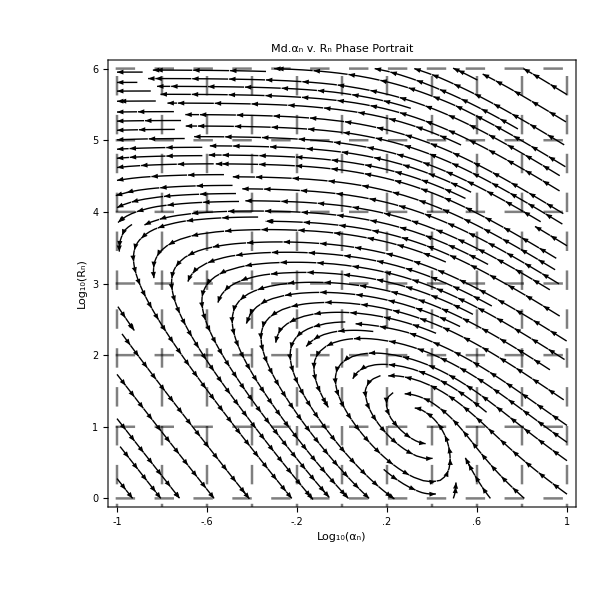

```mathematica
PhasePlaneSK["Md.",600,25]
```

# 13) Define the SK fixed line (precomputed

```mathematica
FixedLineSK={2 √(1/3 (1+√7)),8/27 (-5+17 √7)};
```

# 14) Plot the SK fixed line

### Fixed line legend

```mathematica
FixedLineLegendSK[FL_,FLColor_,TextSize_,MarkerSize_]:=SwatchLegend[{FLColor},{Style[Subscript["SK Γ^*",ToString[FL]],TextSize]},LegendMarkers->{"○",MarkerSize}]
```

### Fixed line in αn-Rn space

```mathematica
FixedLineαRPlaneSK[FLColor_]:=ListPlot[{FixedLineSK},ScalingFunctions->{"Log10","Log10"},PlotRange->{{.1,10},{1,1000000}},PlotStyle->{{FLColor}},PlotMarkers->{{"OpenMarkers",15}}]
```

# 11) Set SK null surfaces (precomputed

### αn null surface ((α̇)_n==0->R_nα(α_n) ==...)

```mathematica
αnNullSurfaceSK[αn_]=-(32 (-64-40 αn^2-8 αn^4+αn^6))/(αn^2 (64+20 αn^2+αn^4));
```

### Rn null surface ((Ṙ)_n==0->R_nR(α_n,τ_n) ==...)

```mathematica
RnNullSurfaceSK[αn_]=-(32 (-128-64 αn^2+6 αn^4+αn^6))/(αn^4 (16+αn^2));
```

### τn null surface ((τ̇)_n==0->R_nτ(α_n) ==...)

```mathematica
τnNullSurfaceSK[αn_]=-(4 (-64-48 αn^2+5 αn^4))/(αn^2 (-4+αn^2));
```

# 12) Plot SK null surfaces

### Null surface legends

```mathematica
NullSurfaceLegendSK[SK_,Color_,TextSize_]:=LineLegend[{{Color,Thickness[.05]},Directive[Color,Dashed,Thickness[.05]],Directive[Color,Dotted,Thickness[.05]]},{Style[ToString[Subscript["α",ToString[SK]],StandardForm]<>"- Null Surf.",TextSize],Style[ToString[Subscript["R",ToString[SK]],StandardForm]<>"- Null Surf.",TextSize],Style[ToString[Subscript["τ",ToString[SK]],StandardForm]<>"- Null Surf.",TextSize]}]
```

### Null surface plots

```mathematica
NullSurfacesSKαRτPlot[Color_]:=Plot[{αnNullSurfaceSK[αn],RnNullSurfaceSK[αn],τnNullSurfaceSK[αn]},{αn,.1,10},ScalingFunctions->{"Log10","Log10"},PlotRange->{{.1,10},{1,1000000}},PlotStyle->{Directive[Thickness[.015],Color],Directive[Dashed,Thickness[.015],Color],Directive[Dotted,Thickness[.02],Color]}]
```

## 15) Define the SK initial conditions for the DoNUTs of interest

### Cloud type

```mathematica
CloudType="Sh. ";
```

### Global initial conditions

```mathematica
νnListSK={1,1,1000,1000,2*114.74};
```

### Parameter initial conditions

```mathematica
wnListSK={3,3,1,1,2};
```

```mathematica
LnListSK={2000,500,500,2000,1102.38};
```

```mathematica
HnListSK={500,2000,2000,500,500};
```

### Implicit parameter initial conditons

```mathematica
αnListSK=SetPrecision[N[LnListSK/HnListSK],3]
```

{4.,0.25,0.25,4.,2.2}

```mathematica
RnListSK=SetPrecision[N[(ⅇ*wnListSK*HnListSK)/νnListSK],3]
```

{4080.,16300.,5.44,1.36,11.8}

```mathematica
τnListSK=SetPrecision[N[HnListSK/wnListSK],3]
```

{167.,667.,2000.,500.,250.}

### Circulation initial conditions

```mathematica
ΓnListSK=SetPrecision[N[ΓnDef[wnListSK,LnListSK,HnListSK]],3]
```

{20400.,16600.,5520.,6800.,6020.}

```mathematica
ΓnνListSK=SetPrecision[N[ΓnDef[wnListSK,LnListSK,HnListSK]/νnListSK],3]
```

{20400.,16600.,5.52,6.8,26.2}

# 16) Plot SK explicit time plots (test trajectories)

### Set the appropriate color scheme for DoNUT choice

```mathematica
DefaultColorArray=ColorData[97,"ColorList"]//InputForm;
```

### SK trajectory legend

```mathematica
SKTrajectoryLegend[TextSize_,MarkerSize_]:=LineLegend[Table[Directive[{DefaultColorArray[[1]][[i]],Thickness[.05]}],{i,1,Length[νnListSK]}],Table[Style[CloudType<>TextString[i],TextSize],{i,1,Length[νnListSK]}],LegendMarkerSize->MarkerSize]
```

## SK trajectories

```mathematica
SKTrajectory=ParametricPlot[Evaluate[Table[{DαnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],DRnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]]},{i,1,Length[νnListSK]}]],{t,tInitial,tFinal},ScalingFunctions->{"Log10","Log10"},Frame->False,PlotStyle->Thickness[.015]];
```

# 17) Define the appropriate polygon

```mathematica
TestSKPoints=Log10[{{DαnSKI[tInitial,νnListSK[[1]],wnListSK[[1]],LnListSK[[1]],HnListSK[[1]]],DRnSKI[tInitial,νnListSK[[1]],wnListSK[[1]],LnListSK[[1]],HnListSK[[1]]]},{DαnSKI[tInitial,νnListSK[[2]],wnListSK[[2]],LnListSK[[2]],HnListSK[[2]]],DRnSKI[tInitial,νnListSK[[2]],wnListSK[[2]],LnListSK[[2]],HnListSK[[2]]]},{DαnSKI[tInitial,νnListSK[[3]],wnListSK[[3]],LnListSK[[3]],HnListSK[[3]]],DRnSKI[tInitial,νnListSK[[3]],wnListSK[[3]],LnListSK[[3]],HnListSK[[3]]]},{DαnSKI[tInitial,νnListSK[[4]],wnListSK[[4]],LnListSK[[4]],HnListSK[[4]]],DRnSKI[tInitial,νnListSK[[4]],wnListSK[[4]],LnListSK[[4]],HnListSK[[4]]]}}];
```

```mathematica
SKPolygone=Graphics[{Pink,Opacity[.2],Polygon[TestSKPoints]}];
```

# 17) Final SK phase portrait for editing

### SK null surface color

```mathematica
SKColor=Blue;
```

### Generate the final phase portrait

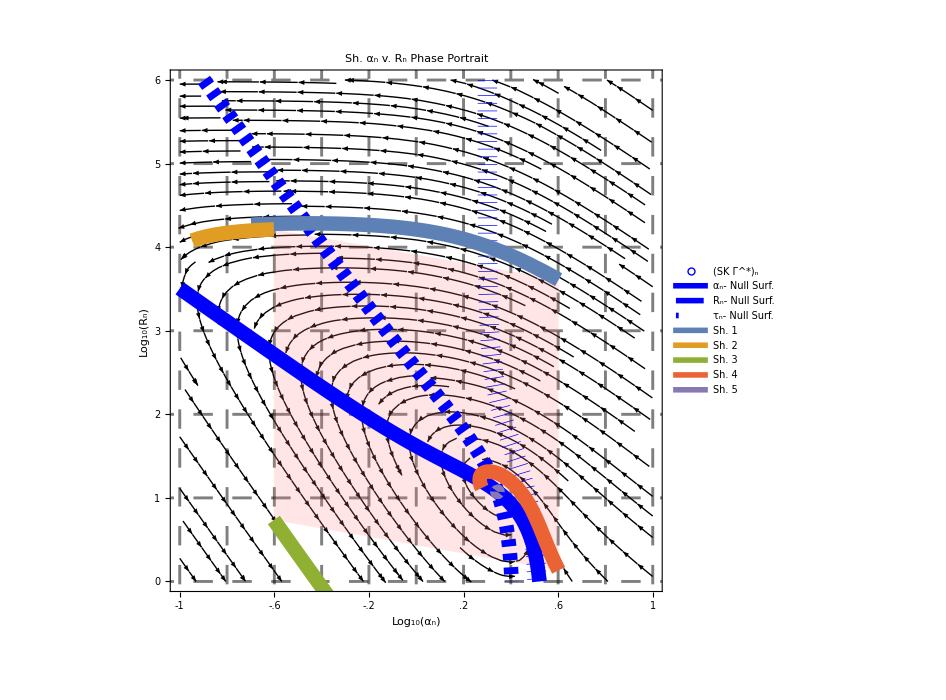

```mathematica
Legended[Show[PhasePlaneSK[CloudType,700,25],SKPolygone,NullSurfacesSKαRτPlot[SKColor],FixedLineαRPlaneSK[SKColor],SKTrajectory],{FixedLineLegendSK[n,SKColor ,24,30],NullSurfaceLegendSK[n,SKColor,24],SKTrajectoryLegend[24,30]}]
```

## 18) Define objects that are used in implicit time plots

### Define the cumulus line, here a w_*=1m/s

```mathematica
CumulusLine=1;
```

```mathematica
CumulusLineStyle={Black,DotDashed,Thickness[.015]};
```

```mathematica
CumulusLinePlot=Plot[CumulusLine,{t,tInitial,tFinal},PlotStyle->CumulusLineStyle];
```

```mathematica
CumulusLineLegend[TextSize_,MarkerSize_]:=LineLegend[{Directive[Thickness[.03],Black,DotDashed]},{Style["Cumulus Threshold",TextSize]},LegendMarkerSize->MarkerSize]
```

```mathematica
CumulusLineLegend[24,40]
```

## Ranges for explicit plot

### wn plot range

```mathematica
wPlotMinSK=0;
```

```mathematica
wPlotMaxSK=6.5;
```

### Ln plot range

```mathematica
LPlotMinSK=0;
```

```mathematica
LPlotMaxSK=11000;
```

### Hn plot range

```mathematica
HPlotMinSK=0;
```

```mathematica
HPlotMaxSK=5500;
```

### αn plot range

```mathematica
αPlotMinSK=0;
```

```mathematica
αPlotMaxSK=4.2;
```

### Rn plot range

```mathematica
RPlotMinSK=.001;
```

```mathematica
RPlotMaxSK=10^6;
```

### τn plot range

```mathematica
τPlotMinSK=1;
```

```mathematica
τPlotMaxSK=5*10^7;
```

### Γn plot range

```mathematica
ΓPlotMinSK=0;
```

```mathematica
ΓPlotMaxSK=55000;
```

### σn plot range

```mathematica
σPlotMinSK=1;
```

```mathematica
σPlotMaxSK=10^11;
```

## Plot Styling

### Frame Style

```mathematica
AxesThickness=Bold;
```

```mathematica
AxesSize=20;
```

### Label Size

```mathematica
LabelSize=20;
```

## 19) Generate Implicit Time Plots

### wn v. Time Plot

```mathematica
wnPlotSK[label_,ExplicitImageSize_]:=Show[Plot[{Evaluate[{Table[wnNumericSolveSK[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{wPlotMinSK,wPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","w_(*n) (m s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize], LabelStyle->Directive[20],PlotLabel->Style["("<>ToString[label]<>") SK_nMax Vertical Velocity",Bold],PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize],CumulusLinePlot];
```

### Ln v. Time Plot

```mathematica
LnPlotSK[label_,ExplicitImageSize_]:=Plot[{Evaluate[{Table[LnNumericSolveSK[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{LPlotMinSK,LPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","L_n (m)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize], LabelStyle->Directive[20],PlotLabel->Style["("<>ToString[label]<>") SK_nUpdraft Radius",Bold],PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize];
```

### Hn v. Time Plot

```mathematica
HnPlotSK[label_,ExplicitImageSize_]:=Plot[{Evaluate[{Table[HnNumericSolveSK[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{HPlotMinSK,HPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","H_n (m)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") SK_nMax Vertical Velocity Height",Bold], PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize];
```

### αn v. Time Plot

```mathematica
αnPlotSK[label_,ExplicitImageSize_]:=Plot[{Evaluate[{Table[DαnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{αPlotMinSK,αPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","α_n"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") SK_nGeometric Aspect Ratio",Bold], PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize];
```

### Rn v. Time Plot

```mathematica
RnPlotSK[label_,ExplicitImageSize_]:=LogPlot[{Evaluate[{Table[DRnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{RPlotMinSK,RPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","R_n"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") SK_nTurbulent Reynolds Number",Bold],PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize]
```

### τn v. Time Plot

```mathematica
τnPlotSK[label_,ExplicitImageSize_]:=LogPlot[{Evaluate[{Table[DτnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{τPlotMinSK,τPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","τ_n (s)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") SK_nTurnover Time",Bold], PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize];
```

### Γn v. Time Plot

```mathematica
ΓnPlotSK[label_,ExplicitImageSize_]:=Plot[{Evaluate[{Table[DΓnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΓPlotMinSK,ΓPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","Γ_n (m^2 s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") SK_nCirculation",Bold], PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize];
```

### σn v. Time Plot

```mathematica
σnPlotSK[label_,ExplicitImageSize_]:=LogPlot[{Evaluate[{Table[DσnSKI[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],{i,1,Length[νnListSK]}]}]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{σPlotMinSK,σPlotMaxSK}},PlotLegends->None,AxesLabel->{"t (s)","σ_n (m^3 s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") SK_nIntergated Kinematic Mass Flux",Bold], PlotStyle->Thickness[.015],GridLines->Automatic,ImageSize->ExplicitImageSize];
```

```mathematica
σnPlotSK[a,100]
```

Part::partw: Part 5 of {10.,10.,3.,3.} does not exist.

Part::partw: Part 5 of {4500.,1500.,1500.,4500.} does not exist.

Part::partw: Part 5 of {1500.,4500.,4500.,1500.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

# 21) Generate a graphics grid containing all of the relevant plots

### Set the Explicit Image Size

```mathematica
ExplicitImageSize=1000;
```

### Generate the Explicit Legend

```mathematica
ExplicitLegendSK=Grid[{{SKTrajectoryLegend[24,30]},{CumulusLineLegend[24,40]}},Alignment->Left];
```

Part::partw: Part 5 of {10.,10.,3.,3.} does not exist.

Part::partw: Part 5 of {4500.,1500.,1500.,4500.} does not exist.

Part::partw: Part 5 of {1500.,4500.,4500.,1500.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

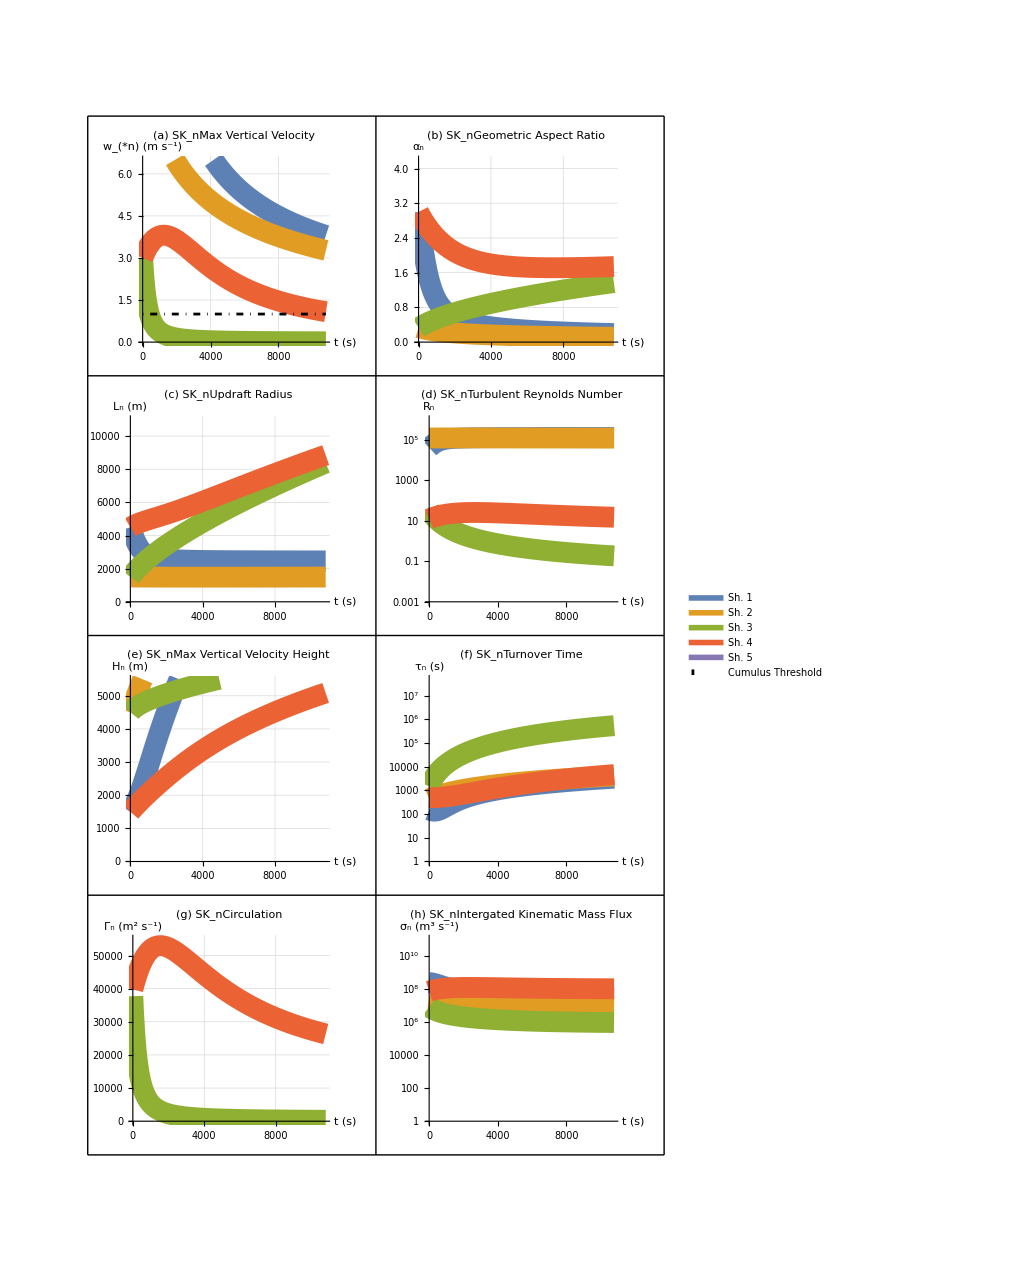
-Graphics-Sh. Explicit Temporal Evolution

```mathematica
Legended[Labeled[GraphicsGrid[{{wnPlotSK[a,ExplicitImageSize],αnPlotSK[b,ExplicitImageSize]},{LnPlotSK[c,ExplicitImageSize],RnPlotSK[d,ExplicitImageSize]},{HnPlotSK[e,ExplicitImageSize],τnPlotSK[f,ExplicitImageSize]},{ΓnPlotSK[g,ExplicitImageSize],σnPlotSK[h,ExplicitImageSize]}},Frame->All,ImageSize->ExplicitImageSize],Text[Style[ToString[CloudType]<>"Explicit Temporal Evolution",FontSize->40]],{{Top,Center}}],ExplicitLegendSK]
```

# 1) Set base form viscous DK dynamical system (precomputed

```mathematica
Mℛ0equivDK[νn_,wn_[t_],Ln_[t_],Hn_[t_],xn_[t_], yn_[t_],wf_[t_],Lf_[t_],Hf_[t_],xf_[t_],yf_[t_]]=Hn[t] (4 Hn[t] Ln[t]^2 wn[t] Hn'[t]+2 Ln[t]^2 wn[t] (4 νn+Ln[t] Ln'[t])+Ln[t]^4 wn'[t]+4 Hn[t]^2 (8 νn wn[t]+Ln[t]^2 wn'[t]))==(Ln[t]^4 wn[t] (3 νn+Hn[t] Hn'[t]))/Hn[t];
```

### DK Mx^1 equivalence

```mathematica
Mx1equivDK[νn_,wn_[t_],Ln_[t_],Hn_[t_],xn_[t_], yn_[t_],wf_[t_],Lf_[t_],Hf_[t_],xf_[t_],yf_[t_]]=1/4 ⅇ (4 wn[t] xn[t] Hn'[t]-(Ln[t]^2 wn[t] xn[t] Hn'[t])/Hn[t]^2+4 Hn[t] (xn[t] wn'[t]+wn[t] xn'[t])+(Ln[t] (Ln[t] xn[t] wn'[t]+wn[t] (2 xn[t] Ln'[t]+Ln[t] xn'[t])))/Hn[t])==-(ⅇ νn (32 Hn[t]^4+8 Hn[t]^2 Ln[t]^2-3 Ln[t]^4) wn[t] xn[t])/(4 Hn[t]^3 Ln[t]^2)+1/(8 Hn[t] (Hf[t]+Hn[t])^3 Lf[t]^4)ⅇ^(-(-2 Lf[t]^2+(xf[t]-xn[t])^2+(yf[t]-yn[t])^2)/Lf[t]^2) Hf[t] wf[t] wn[t] (xf[t]-xn[t]) (-4 Hn[t]^3 Lf[t]^4+3 Hn[t] Ln[t]^2 (Lf[t]^4-2 Lf[t]^2 Ln[t]^2+Ln[t]^2 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2))+Hf[t] (4 Hn[t]^2 Lf[t]^4+Lf[t]^4 Ln[t]^2-2 Lf[t]^2 Ln[t]^4+Ln[t]^4 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2)))+1/(32 Hn[t] (Hf[t]+Hn[t])^3 Lf[t]^4)ⅇ^(2-((xf[t]-xn[t])^2+(yf[t]-yn[t])^2)/Lf[t]^2) Hf[t] wf[t] wn[t] (xf[t]-xn[t]) (Hn[t] (8 Hn[t]^2 Lf[t]^4-6 Lf[t]^4 Ln[t]^2+6 Lf[t]^2 Ln[t]^4-3 Ln[t]^4 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2))-Hf[t] (8 Hn[t]^2 Lf[t]^4+2 Lf[t]^4 Ln[t]^2-2 Lf[t]^2 Ln[t]^4+Ln[t]^4 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2)));
```

### DK My^1 equivalence

```mathematica
My1equivDK[νn_,wn_[t_],Ln_[t_],Hn_[t_],xn_[t_], yn_[t_],wf_[t_],Lf_[t_],Hf_[t_],xf_[t_],yf_[t_]]=1/4 ⅇ (4 wn[t] yn[t] Hn'[t]-(Ln[t]^2 wn[t] yn[t] Hn'[t])/Hn[t]^2+4 Hn[t] (yn[t] wn'[t]+wn[t] yn'[t])+(Ln[t] (Ln[t] yn[t] wn'[t]+wn[t] (2 yn[t] Ln'[t]+Ln[t] yn'[t])))/Hn[t])==1/(8 Hn[t] (Hf[t]+Hn[t])^3 Lf[t]^4)ⅇ^(-(-2 Lf[t]^2+(xf[t]-xn[t])^2+(yf[t]-yn[t])^2)/Lf[t]^2) Hf[t] wf[t] wn[t] (-4 Hn[t]^3 Lf[t]^4+3 Hn[t] Ln[t]^2 (Lf[t]^4-2 Lf[t]^2 Ln[t]^2+Ln[t]^2 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2))+Hf[t] (4 Hn[t]^2 Lf[t]^4+Lf[t]^4 Ln[t]^2-2 Lf[t]^2 Ln[t]^4+Ln[t]^4 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2))) (yf[t]-yn[t])+1/(32 Hn[t] (Hf[t]+Hn[t])^3 Lf[t]^4)ⅇ^(2-((xf[t]-xn[t])^2+(yf[t]-yn[t])^2)/Lf[t]^2) Hf[t] wf[t] wn[t] (Hn[t] (8 Hn[t]^2 Lf[t]^4-6 Lf[t]^4 Ln[t]^2+6 Lf[t]^2 Ln[t]^4-3 Ln[t]^4 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2))-Hf[t] (8 Hn[t]^2 Lf[t]^4+2 Lf[t]^4 Ln[t]^2-2 Lf[t]^2 Ln[t]^4+Ln[t]^4 ((xf[t]-xn[t])^2+(yf[t]-yn[t])^2))) (yf[t]-yn[t])-(ⅇ νn (32 Hn[t]^4+8 Hn[t]^2 Ln[t]^2-3 Ln[t]^4) wn[t] yn[t])/(4 Hn[t]^3 Ln[t]^2);
```

### DK Mz^1 equivalence

```mathematica
Mz1equivDK[νn_,wn_[t_],Ln_[t_],Hn_[t_],xn_[t_], yn_[t_],wf_[t_],Lf_[t_],Hf_[t_],xf_[t_],yf_[t_]]=2 ⅇ Hn[t] (2 wn[t] Hn'[t]+Hn[t] wn'[t])==1/(64 Hn[t]^2)ⅇ wn[t] ((32 νn (-32 Hn[t]^4+Ln[t]^4))/Ln[t]^2+ⅇ Hn[t] (8 Hn[t]^2+Ln[t]^2) wn[t]-(32 ⅇ^(-(-Lf[t]^2+(xf[t]-xn[t])^2+(yf[t]-yn[t])^2)/Lf[t]^2) Hf[t] Hn[t]^3 (4 Hf[t] Hn[t]+Ln[t]^2) wf[t] (-Lf[t]^2+(xf[t]-xn[t])^2+(yf[t]-yn[t])^2))/((Hf[t]+Hn[t])^3 Lf[t]^2));
```

### DK Mℛ^2 equivalence

```mathematica
Mℛ2equivDK[νn_,wn_[t_],Ln_[t_],Hn_[t_],xn_[t_], yn_[t_],wf_[t_],Lf_[t_],Hf_[t_],xf_[t_],yf_[t_]]=1/(32 Hn[t]^3)ⅇ Ln[t]^3 (-Ln[t] wn[t] (24 νn-ⅇ Hn[t] wn[t]-(8 ⅇ^(-(-Lf[t]^2+(xf[t]-xn[t])^2+(yf[t]-yn[t])^2)/Lf[t]^2) Hf[t] Hn[t]^2 (Hf[t]+3 Hn[t]) wf[t] (Lf[t]^2-(xf[t]-xn[t])^2-(yf[t]-yn[t])^2))/((Hf[t]+Hn[t])^3 Lf[t]^2))+8 Hn[t] (4 Hn[t] wn[t] Ln'[t]+Ln[t] (-wn[t] Hn'[t]+Hn[t] wn'[t])))==0;
```

# 2) Solve Viscous DK dynamical system

## Clear previous system

```mathematica
ClearAll[SKDynamicSystemSolve]
```

## Set DK dynamical system

```mathematica
DKDynamicSystemSolve=ParametricNDSolve[{Mℛ0equivDK[νn,wn[t],Ln[t],Hn[t],xn[t], yn[t],wf[t],Lf[t],Hf[t],xf[t],yf[t]],Mx1equivDK[νn,wn[t],Ln[t],Hn[t],xn[t], yn[t],wf[t],Lf[t],Hf[t],xf[t],yf[t]],My1equivDK[νn,wn[t],Ln[t],Hn[t],xn[t], yn[t],wf[t],Lf[t],Hf[t],xf[t],yf[t]],Mz1equivDK[νn,wn[t],Ln[t],Hn[t],xn[t], yn[t],wf[t],Lf[t],Hf[t],xf[t],yf[t]],wn[0]==wnInitial,Ln[0]==LnInitial,Hn[0]==HnInitial,xn[0]==xnInitial,yn[0]==ynInitial,Mℛ2equivDK[νn,wn[t],Ln[t],Hn[t],xn[t], yn[t],wf[t],Lf[t],Hf[t],xf[t],yf[t]],Mℛ0equivDK[νf,wf[t],Lf[t],Hf[t],xf[t], yf[t],wn[t],Ln[t],Hn[t],xn[t],yn[t]],Mx1equivDK[νf,wf[t],Lf[t],Hf[t],xf[t], yf[t],wn[t],Ln[t],Hn[t],xn[t],yn[t]],My1equivDK[νf,wf[t],Lf[t],Hf[t],xf[t], yf[t],wn[t],Ln[t],Hn[t],xn[t],yn[t]],Mz1equivDK[νf,wf[t],Lf[t],Hf[t],xf[t], yf[t],wn[t],Ln[t],Hn[t],xn[t],yn[t]],Mℛ2equivDK[νf,wf[t],Lf[t],Hf[t],xf[t], yf[t],wn[t],Ln[t],Hn[t],xn[t],yn[t]],wf[0]==wfInitial,Lf[0]==LfInitial,Hf[0]==HfInitial,xf[0]==xfInitial,yf[0]==yfInitial},{wn,Ln,Hn,xn,yn,wf,Lf,Hf,xf,yf},{t,tInitial,tFinal},{νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial}, Method->{"EquationSimplification"->"Residual"}]
```

{wn→ParametricFunction[<>],Ln→ParametricFunction[<>],Hn→ParametricFunction[<>],xn→ParametricFunction[<>],yn→ParametricFunction[<>],wf→ParametricFunction[<>],Lf→ParametricFunction[<>],Hf→ParametricFunction[<>],xf→ParametricFunction[<>],yf→ParametricFunction[<>]}

# 3) Set explicit DK explicit parameters

## DoNUT_n

### wn tendency - ((ẇ)_n)

```mathematica
wnNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=wn[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### Ln tendency - ((L̇)_n)

```mathematica
LnNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=Ln[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### Hn tendency - ((Ḣ)_n)

```mathematica
HnNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=Hn[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### xn tendency - ((ẋ)_n)

```mathematica
xnNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=xn[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### yn tendency - ((ẏ)_n)

```mathematica
ynNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=yn[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

## DoNUT_f

### wf tendency - ((ẇ)_f)

```mathematica
wfNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=wf[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### Lf tendency - ((L̇)_f)

```mathematica
LfNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=Lf[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### Hf tendency - ((Ḣ)_f)

```mathematica
HfNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=Hf[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### xf tendency - ((ẋ)_f)

```mathematica
xfNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=xf[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

### yf tendency - ((ẏ)_f)

```mathematica
yfNumericSolveDK[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=yf[νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial][t]/.DKDynamicSystemSolve;
```

# 4) Define the implicit the remaining DK parameter tendencies

```mathematica
ClearAll[d]
```

### d- (d)

```mathematica
dDef[xn_,yn_,xf_,yf_]=((xf-xn)^2+(yf-yn)^2)^(1/2);
```

### Λnf - (Λ_nf)

```mathematica
ΛnfDef[d_,Lf_]=d/Lf;
```

### Πnf - (Π_nf)

```mathematica
ΠnfDef[Hn_,Hf_]=Hn/Hf;
```

### Υnf - (Υ_nf)

```mathematica
ΥnfDef[Ln_,Lf_]=Ln/Lf;
```

### Ξnf-(Ξ_nf)

```mathematica
ΞnfDef[wn_,wf_]=wn/wf;
```

# 5) Define numeric tendencies for DK implicit parameters

### αn tendency - ((α̇)_n)

```mathematica
DαnDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=αnDef[LnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],HnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### Rn tendency - ((Ṙ)_n)

```mathematica
DRnDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=RnDef[νn,wnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],HnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### τn tendency - ((τ̇)_n)

```mathematica
DτnDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=τnDef[wnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],HnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### dnf tendency - (ḋ)

```mathematica
DdDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=dDef[xnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],ynNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],xfNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],yfNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### Λnf tendency - (Λ̇)

```mathematica
DΛnfDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=ΛnfDef[DdDKI[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],LfNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### Πnf tendency - (Π̇)

```mathematica
DΠnfDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=ΠnfDef[HnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],HfNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### Ξnf tendency - (Ξ̇)

```mathematica
DΞnfDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=ΞnfDef[wnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],wfNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### Υnf tendency - (Υ̇)

```mathematica
DΥnfDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=ΥnfDef[LnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],LfNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

# 6) Set the implicit DK quantities of interest from numeric integrate

### Γn (Γ_n)

```mathematica
DΓnDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=ΓnDef[wnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],LnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],HnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

### σn (σ_n)

```mathematica
DσnDKI[t_,νn_,wnInitial_,LnInitial_,HnInitial_,xnInitial_,ynInitial_,νf_,wfInitial_,LfInitial_,HfInitial_,xfInitial_,yfInitial_]=σnDef[wnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial],LnNumericSolveDK[t,νn,wnInitial,LnInitial,HnInitial,xnInitial,ynInitial,νf,wfInitial,LfInitial,HfInitial,xfInitial,yfInitial]];
```

# 7) Set the implicit DK parameter tendencies (precomputed

### αn tendency ((α̇)_n)

```mathematica
DαnDK[τn_,αn_,Rn_, Λ_,Π_,Ξ_]=-(ⅇ αn (64+20 αn^2+αn^4))/(128 (8+3 αn^2) τn)+(ⅇ^(1-Λ^2) αn (4+αn^2) (-1+Λ^2) Π (6+(6+αn^2) Π))/(4 (8+3 αn^2) Ξ (1+Π)^3 τn)+(64 ⅇ+40 ⅇ αn^2+8 ⅇ αn^4-ⅇ αn^6)/(Rn (32 αn τn+12 αn^3 τn));
```

### Rn tendency ((Ṙ)_n)

```mathematica
DRnDK[τn_,αn_,Rn_,  Λ_,Π_,Ξ_]=(ⅇ Rn αn^2 (16+αn^2))/(64 (8+3 αn^2) τn)+(ⅇ (-128-64 αn^2+6 αn^4+αn^6))/(2 αn^2 (8+3 αn^2) τn)-(ⅇ^(1-Λ^2) Rn αn^2 (-1+Λ^2) Π (6+(6+αn^2) Π))/(2 (8+3 αn^2) Ξ (1+Π)^3 τn);
```

### τn tendency ((τ̇)_n)

```mathematica
DτnDK[αn_,Rn_,  Λ_,Π_,Ξ_]=-(ⅇ (-4+αn^2))/(4 (8+3 αn^2))+(ⅇ (64+48 αn^2-5 αn^4))/(Rn αn^2 (8+3 αn^2))+(ⅇ^(1-Λ^2) (-1+Λ^2) Ξ (-16+αn^2 (3+5 Π)))/((8+3 αn^2) (1+Π)^3);
```

# 12) Generate DK Phase Space

## Generate the time implicit phase plane

### Label Size

```mathematica
PhasePlaneDK[Λ_,Π_,Ξ_,DK_,time_,label_]:=StreamPlot[{DαnDK[1,αn,Rn, Λ,Π,Ξ],DRnDK[1,αn,Rn, Λ,Π,Ξ]},{αn,.1,10},{Rn,1,1000000},ScalingFunctions->{"Log10","Log10"},PlotLegends->Automatic,FrameTicks->{{{{10^0,"0"},{10^1,"1"},{10^2,"2"},{10^3,"3"},{10^4,"4"},{10^5,"5"},{10^6,"6"}},{{10^0,"0"},{10^1,"1"},{10^2,"2"},{10^3,"3"},{10^4,"4"},{10^5,"5"},{10^6,"6"}}},{{{10^-1,"-1"},{10^(-.8),"-.8"},{10^(-.6),"-.6"},{10^(-.4),"-.4"},{10^(-.2),"-.2"},{10^0,"0"},{10^(.2),".2"},{10^(.4),".4"},{10^(.6),".6"},{10^(.8),".8"},{10^1,"1"}},{{10^-1,"-1"},{10^(-.8),"-.8"},{10^(-.6),"-.6"},{10^(-.4),"-.4"},{10^(-.2),"-.2"},{10^0,"0"},{10^(.2),".2"},{10^(.4),".4"},{10^(.6),".6"},{10^(.8),".8"},{10^1,"1"}}}},FrameTicksStyle->{GrayLevel[0],Bold,"Large"},StreamColorFunction->None,PlotTheme->"Detailed",ImageSize->Large,StreamStyle->Black,FrameLabel->{"Log_10("<>ToString[Subscript[α,DK],TraditionalForm]<>")","Log_10("<>ToString[Subscript[R,DK],TraditionalForm]<>")"}, PlotLabel->"("<>ToString[label]<>")  "<>ToString[Subscript[α,DK],TraditionalForm] <>" v. " ToString[Subscript[R,DK],TraditionalForm]<>" Phase Portrait, t="<>ToString[time]<>"s",LabelStyle->{GrayLevel[0],"Large"},GridLines->{{-1,-.8,-.6,-.4,-.2,0,.2,.4,.6,.8,1},{0,1,2,3,4,5,6}},GridLinesStyle->Directive[Black,Opacity[.5],Dashing[Large],Thickness[.003]],FrameStyle->Bold]
```

# 13) Set DK null surfaces (precomputed

### Set αn null surface ((α̇)_n==0->R_nα(α_n),=...)

```mathematica
αnNullSurfaceDK[τn_,αn_,Λ_, Π_,Ξ_]=-(32 ⅇ^(Λ^2) (-64-40 αn^2-8 αn^4+αn^6) Ξ (1+Π)^3)/(αn^2 (4+αn^2) (ⅇ^(Λ^2) (16+αn^2) Ξ (1+Π)^3-32 (-1+Λ^2) Π (6+(6+αn^2) Π)));
```

### Set Rn null surface ((Ṙ)_n==0->R_nR(α_n,)=...)

```mathematica
RnNullSurfaceDK[τn_,αn_,Λ_, Π_,Ξ_]=-(32 ⅇ^(Λ^2) (-128-64 αn^2+6 αn^4+αn^6) Ξ (1+Π)^3)/(αn^4 (ⅇ^(Λ^2) (16+αn^2) Ξ (1+Π)^3-32 (-1+Λ^2) Π (6+(6+αn^2) Π)));
```

### Set τn null surface ((τ̇)_n==0->R_nRτ(α_n,)=...)

```mathematica
τnNullSurfaceDK[αn_,Λ_, Π_,Ξ_]=-(4 ⅇ^(Λ^2) (-64-48 αn^2+5 αn^4) (1+Π)^3)/(αn^2 (ⅇ^(Λ^2) (-4+αn^2) (1+Π)^3-4 (-1+Λ^2) Ξ (-16+αn^2 (3+5 Π))));
```

## Generate the near field DK null surfaces plot

### Null surface legends

```mathematica
NullSurfaceLegendDK[DK_,Color_]:=LineLegend[{Directive[Color,Thickness[.05]],Directive[Color,Dashed,Thickness[.05]],Directive[Color,Dotted,Thickness[.05]]},{ToString[Subscript["α",ToString[DK]],StandardForm]<>"- Null Surf.",ToString[Subscript["R",ToString[DK]],StandardForm]<>"- Null Surf.",ToString[Subscript["τ",ToString[DK]],StandardForm]<>"- Null Surf."}]
```

### Null surface plots

```mathematica
NullSurfaceSKDαRτPlot[ Λ_,Π_,Ξ_,Color_]:=Plot[{αnNullSurfaceDK[1,αn,Λ, Π,Ξ],RnNullSurfaceDK[1,αn,Λ, Π,Ξ],τnNullSurfaceDK[αn,Λ, Π,Ξ]},{αn,.1,10},ScalingFunctions->{"Log10","Log10"},PlotRange->{{.1,10},{1,1000000}},PlotStyle->{Directive[Color,Thickness[.015]],Directive[Color,Dashed,Thickness[.015]],Directive[Color,Dotted,Thickness[.02]]}];
```

## Define the DK fixed line (precomputed

### Set the fixed line

```mathematica
FixedLine1DK[Λ_,Π_,Ξ_]={2 √(1/3 (1+√7)),(16 (32+17 √7) ⅇ^(Λ^2) Ξ (1+Π)^3)/((4+√7) ((13+√7) ⅇ^(Λ^2) Ξ (1+Π)^3-16 (-1+Λ^2) Π (9+(11+2 √7) Π)))};
```

# Generate the near field DK fixed line plot

### Fixed line Legend

```mathematica
FixedLineLegendDK[FL_,FLColor_]:=PointLegend[{FLColor},{Subscript["DK Γ^*",ToString[FL]]},LegendMarkerSize->25]
```

### Fixed line in αn-Rn space

```mathematica
FixedLineαRPlaneDK[Λ_,Π_,Ξ_,FLColor_]:=ListPlot[{FixedLine1DK[Λ,Π,Ξ]},ScalingFunctions->{"Log10","Log10"},PlotRange->{{.1,10},{1,1000000}},PlotStyle->{{FLColor}},PlotMarkers->{Automatic,28}]
```

# 18) Define the DK initial conditions for the DoNUTs of interest

## Test DK_i set

## Shallow test SK set

## Sh. test cases

```mathematica
νnListSK={1,1,1000,1000,2*114.74};
```

```mathematica
wnListSK={10,10,3,3};
```

```mathematica
LnListSK={4500,1500,1500,4500};
```

```mathematica
HnListSK={1500,4500,4500,1500};
```

### Set the DoNUT of choice

```mathematica
nTestDoNUTDK=2;
```

### Set the appropriate color scheme for DoNUT choice

```mathematica
DefaultColorArray=ColorData[97,"ColorList"]//InputForm;
```

```mathematica
nTestDoNUTColor=DefaultColorArray[[1]][[nTestDoNUTDK]];
```

## DoNUT_n Initialization

```mathematica
νnDK=νnListSK[[nTestDoNUTDK]];
```

```mathematica
wnDK=wnListSK[[nTestDoNUTDK]];
```

```mathematica
LnDK=LnListSK[[nTestDoNUTDK]];
```

```mathematica
HnDK=HnListSK[[nTestDoNUTDK]];
```

```mathematica
xnDK=0;
```

```mathematica
ynDK=0;
```

## Define the far field cloud type parameter ranges

### Far field range

```mathematica
wfDKMin=1;
```

```mathematica
wfDKMax=3;
```

```mathematica
LfDKMin=500;
```

```mathematica
LfDKMax=2000;
```

```mathematica
HfDKMin=500;
```

```mathematica
HfDKMax=2000;
```

## Generate the manipulable initial phase portrait to look for interesting cases of interaction

```mathematica
Legended[Manipulate[GraphicsGrid[{{Show[PhasePlaneDK[2,HnDK/Hf,wnDK/wf,i,tInitial,a],NullSurfaceSKDαRτPlot[2,HnDK/Hf,wnDK/wf,Magenta],FixedLineαRPlaneSK[Magenta],FixedLineαRPlaneDK[2,HnDK/Hf,wnDK/wf,Magenta]],Show[PhasePlaneDK[2,Hf/HnDK,wf/wnDK,j,tInitial,b],NullSurfaceSKDαRτPlot[2,Hf/HnDK,wf/wnDK,Green],FixedLineαRPlaneSK[Green],FixedLineαRPlaneDK[2,Hf/HnDK,wf/wnDK,Green]]}}],{Hf,HfDKMin,HfDKMax},{wf,wfDKMin,wfDKMax}],{FixedLineLegendSK[i,Magenta],FixedLineLegendDK[i,Magenta],NullSurfaceLegendDK[i,Magenta],FixedLineLegendSK[j,Green],FixedLineLegendDK[j,Green],NullSurfaceLegendDK[j,Green]}];
```

## Define the far field DK of interest leaving Lf arbitrary

```mathematica
wfDK=30
```

30

```mathematica
HfDK=4000
```

4000

```mathematica
dDK[Lf_]:=2*Lf
```

# 21) Set implicit plot ranges

## Near field implicit plot range

### wn plot range

```mathematica
wnPlotMinDK=0;
```

```mathematica
wnPlotMaxDK=10;
```

### Ln plot range

```mathematica
LnPlotMinDK=0;
```

```mathematica
LnPlotMaxDK=2000;
```

### Hn plot range

```mathematica
HnPlotMinDK=0;
```

```mathematica
HnPlotMaxDK=15000;
```

### αn plot range

```mathematica
αnPlotMinDK=0;
```

```mathematica
αnPlotMaxDK=.5;
```

### Rn plot range

```mathematica
RnPlotMinDK=1;
```

```mathematica
RnPlotMaxDK=5*10^6;
```

### τn plot range

```mathematica
τnPlotMinDK=1;
```

```mathematica
τnPlotMaxDK=5000;
```

### Γn plot range

```mathematica
ΓnPlotMinDK=0;
```

```mathematica
ΓnPlotMaxDK=200000;
```

### σn plot range

```mathematica
σnPlotMinDK=1;
```

```mathematica
σnPlotMaxDK=5*10^8;
```

### dnf plot range

```mathematica
dnfPlotMinDK=0;
```

```mathematica
dnfPlotMaxDK=9000;
```

### Λnf plot range

```mathematica
ΛnfPlotMinDK=0;
```

```mathematica
ΛnfPlotMaxDK=2.5;
```

### Πnf plot range

```mathematica
ΠnfPlotMinDK=0;
```

```mathematica
ΠnfPlotMaxDK=1.5;
```

### Υnf plot range

```mathematica
ΥnfPlotMinDK=0;
```

```mathematica
ΥnfPlotMaxDK=.6;
```

### Ξnf plot range

```mathematica
ΞnfPlotMinDK=0;
```

```mathematica
ΞnfPlotMaxDK=5;
```

## Far field implicit plot range

### wf plot range

```mathematica
wfPlotMinDK=0;
```

```mathematica
wfPlotMaxDK=30;
```

### Lf plot range

```mathematica
LfPlotMinDK=0;
```

```mathematica
LfPlotMaxDK=4500;
```

### Hf plot range

```mathematica
HfPlotMinDK=0;
```

```mathematica
HfPlotMaxDK=26000;
```

### αf plot range

```mathematica
αfPlotMinDK=0;
```

```mathematica
αfPlotMaxDK=1;
```

### Rf plot range

```mathematica
RfPlotMinDK=1;
```

```mathematica
RfPlotMaxDK=5*10^6;
```

### τf plot range

```mathematica
τfPlotMinDK=1;
```

```mathematica
τfPlotMaxDK=5000;
```

### Γf plot range

```mathematica
ΓfPlotMinDK=0;
```

```mathematica
ΓfPlotMaxDK=5.5*10^5;
```

### σf plot range

```mathematica
σfPlotMinDK=1;
```

```mathematica
σfPlotMaxDK=5*10^9;
```

### dfn plot range

```mathematica
dfnPlotMinDK=0;
```

```mathematica
dfnPlotMaxDK=9000;
```

### Λfn plot range

```mathematica
ΛfnPlotMinDK=0;
```

```mathematica
ΛfnPlotMaxDK=10;
```

### Πfn plot range

```mathematica
ΠfnPlotMinDK=0;
```

```mathematica
ΠfnPlotMaxDK=2;
```

### Υfn plot range

```mathematica
ΥfnPlotMinDK=0;
```

```mathematica
ΥfnPlotMaxDK=3;
```

### Ξfn plot range

```mathematica
ΞfnPlotMinDK=0;
```

```mathematica
ΞfnPlotMaxDK=4;
```

## 21) Generate Explicit time plots

### Define the cumulus line, here a w_*=1m/s

```mathematica
CumulusLine=1;
```

```mathematica
CumulusLineStyle={Black,DotDashed};
```

```mathematica
CumulusLinePlot=Plot[CumulusLine,{t,tInitial,tFinal},PlotStyle->CumulusLineStyle];
```

### Set the plot styles for the SK and DK

```mathematica
PlotStyleSKi={nTestDoNUTColor,Thickness[.015]};
```

```mathematica
PlotStyleSKj={Purple,Thickness[.015]};
```

```mathematica
PlotStyleDKi={nTestDoNUTColor,Dashed,Thickness[.015]};
```

```mathematica
PlotStyleDKj={Purple, Dashed,Thickness[.015]};
```

### Set the plot styles for the SK and DK

```mathematica
PlotLegendStyleSKi={nTestDoNUTColor,Thickness[.05]};
```

```mathematica
PlotLegendStyleSKj={Purple,Thickness[.05]};
```

```mathematica
PlotLegendStyleDKi={nTestDoNUTColor,Dashed,Thickness[.05]};
```

```mathematica
PlotLegendStyleDKj={Purple, Dashed,Thickness[.05]};
```

### Define the Implicit plot labels

```mathematica
ImplicitPlotLegendDKi=LineLegend[{Directive[PlotLegendStyleSKi[[1]],PlotLegendStyleSKi[[2]]],Directive[PlotLegendStyleDKi[[1]],PlotStyleDKi[[2]],PlotLegendStyleDKi[[3]]]},{"SK_i","DK_i"}];
```

```mathematica
ImplicitPlotLegendDKj=LineLegend[{Directive[PlotLegendStyleSKj[[1]],PlotLegendStyleSKj[[2]]],Directive[PlotLegendStyleDKj[[1]],PlotLegendStyleDKj[[2]],PlotLegendStyleDKj[[3]]]},{"SK_j","DK_j"}];
```

### Define the Explicit plot labels

```mathematica
ExplicitPlotLegendDKi=Grid[{{LineLegend[{Directive[PlotLegendStyleSKi[[1]],PlotLegendStyleSKi[[2]]],Directive[PlotLegendStyleDKi[[1]],PlotLegendStyleDKi[[2]],PlotLegendStyleDKi[[3]]]},{Style["SK_i",Large],Style["DK_i",Large]}]},{LineLegend[{Directive[Thickness[.05],Black,DotDashed]},{Style["Cumulus Threshold",Large]}]}},Alignment->Left]
```

```mathematica
ExplicitPlotLegendDKj=LineLegend[{Directive[PlotLegendStyleSKj[[1]],PlotLegendStyleSKj[[2]]],Directive[PlotLegendStyleDKj[[1]],PlotLegendStyleDKj[[2]],PlotLegendStyleDKj[[3]]]},{Style["SK_j",Large],Style["DK_j",Large]}];
```

### Set label style

```mathematica
LabelStyleExplicitPlot=Directive[15] ;
```

## Near field implicit plot generator

### wn v. Time Plot

```mathematica
wnPlotDK[Lf_,label_]:=Show[{Plot[{wnNumericSolveSK[t,νnDK,wnDK,LnDK,HnDK],wnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{wnPlotMinDK,wnPlotMaxDK}},AxesLabel->{"t (s)","w_(*i) (m s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") DK_iMax Vertical Velocity",Bold],PlotStyle->{PlotStyleSKi,PlotStyleDKi}, LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large],CumulusLinePlot}]
```

### Ln v. Time Plot

```mathematica
LnPlotDK[Lf_,label_]:=Plot[{LnNumericSolveSK[t,νnDK,wnDK,LnDK,HnDK],LnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{LnPlotMinDK,LnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},AxesLabel->{"t (s)","L_i (m)"},PlotLabel->Style["("<>ToString[label]<>") DK_iUpdraft Radius",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Hn v. Time Plot

```mathematica
HnPlotDK[Lf_,label_]:=Plot[{HnNumericSolveSK[t,νnDK,wnDK,LnDK,HnDK],HnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{HnPlotMinDK,HnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},AxesLabel->{"t (s)","H_i (m)"},PlotLabel->Style["("<>ToString[label]<>") DK_iMax Vertical Velocity Height",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### αn v. Time Plot

```mathematica
αnPlotDK[Lf_,label_]:=Plot[{DαnSKI[t,νnDK,wnDK,LnDK,HnDK],DαnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{αnPlotMinDK,αnPlotMaxDK}},AxesLabel->{"t (s)","α_i"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iGeometric Aspect Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Rn v. Time Plot

```mathematica
RnPlotDK[Lf_,label_]:=LogPlot[{DRnSKI[t,νnDK,wnDK,LnDK,HnDK],DRnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{1,RnPlotMaxDK}},AxesLabel->{"t (s)","R_i"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iTurbulent Reynolds Number",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic]
```

### τn v. Time Plot

```mathematica
τnPlotDK[Lf_,label_]:=LogPlot[{DτnSKI[t,νnDK,wnDK,LnDK,HnDK],DτnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{τnPlotMinDK,τnPlotMaxDK}},AxesLabel->{"t (s)","τ_i (s)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iTurnover Time",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Γn v. Time Plot

```mathematica
ΓnPlotDK[Lf_,label_]:=Plot[{DΓnSKI[t,νnDK,wnDK,LnDK,HnDK],DΓnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΓnPlotMinDK,ΓnPlotMaxDK}},AxesLabel->{"t (s)","Γ_i (m^2s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iCirculation",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### σn v. Time Plot

```mathematica
σnPlotDK[Lf_,label_]:=LogPlot[{DσnSKI[t,νnDK,wnDK,LnDK,HnDK],DσnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{σnPlotMinDK,σnPlotMaxDK}},AxesLabel->{"t (s)","σ_i (m^3s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKi,PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iKinematic Mass Flux",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large];
```

### dnf v. Time Plot

```mathematica
dnfPlotDK[Lf_,label_]:=Plot[{DdDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{dnfPlotMinDK,dnfPlotMaxDK}},AxesLabel->{"t (s)","d_i(m)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") Separation",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Λnf v. Time Plot

```mathematica
ΛnfPlotDK[Lf_,label_]:=Plot[{DΛnfDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΛnfPlotMinDK,ΛnfPlotMaxDK}},AxesLabel->{"t (s)","Λ_j"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_i Scaled Separation",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Πnf v. Time Plot

```mathematica
ΠnfPlotDK[Lf_,label_]:=Plot[{DΠnfDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΠnfPlotMinDK,ΠnfPlotMaxDK}},AxesLabel->{"t (s)","Π_ij"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iHeight Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Υnf v. Time Plot

```mathematica
ΥnfPlotDK[Lf_,label_]:=Plot[{DΥnfDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΥnfPlotMinDK,ΥnfPlotMaxDK}},AxesLabel->{"t (s)","Υ_ij"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iLength Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Ξnf v. Time Plot

```mathematica
ΞnfPlotDK[Lf_,label_]:=Plot[{DΞnfDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΞnfPlotMinDK,ΞnfPlotMaxDK}},AxesLabel->{"t (s)","Ξ_ij"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleDKi},PlotLabel->Style["("<>ToString[label]<>") DK_iMax Vertical Velocity Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

## Far field implicit plot generator

### wf v . Time Plot

```mathematica
wfPlotDK[Lf_,label_]:=Show[{Plot[{wnNumericSolveSK[t,νnDK,wfDK,Lf,HfDK],wfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{wfPlotMinDK,wfPlotMaxDK}},AxesLabel->{"t (s)","w_(*_j)(m s^-1)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") DK_jMax Vertical Velocity",Bold],PlotStyle->{PlotStyleSKj,PlotStyleDKj}, LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large],CumulusLinePlot}]
```

### Lf v. Time Plot

```mathematica
LfPlotDK[Lf_,label_]:=Plot[{LnNumericSolveSK[t,νnDK,wfDK,Lf,HfDK],LfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{LfPlotMinDK,LfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKj,PlotStyleDKj},AxesLabel->{"t (s)","L_j (m)"},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotLabel->Style["("<>ToString[label]<>") DK_jUpdraft Radius",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Hf v. Time Plot

```mathematica
HfPlotDK[Lf_,label_]:=Plot[{HnNumericSolveSK[t,νnDK,wfDK,Lf,HfDK],HfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,Lf,HfDK,dDK[Lf],0]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{HfPlotMinDK,HfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],PlotStyle->{PlotStyleSKj,PlotStyleDKj},AxesLabel->{"t (s)","H_j (m)"},PlotLabel->Style["("<>ToString[label]<>") DK_jMax Vertical Velocity Height",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### αf v. Time Plot

```mathematica
αfPlotDK[Lf_,label_]:=Plot[{DαnSKI[t,νnDK,wfDK,Lf,HfDK],DαnDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{αfPlotMinDK,αfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","α_j"},PlotStyle->{PlotStyleSKj,PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jGeometric Aspect Ratio", Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Rf v. Time Plot

```mathematica
RfPlotDK[Lf_,label_]:=LogPlot[{DRnSKI[t,νnDK,wfDK,Lf,HfDK],DRnDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{RfPlotMinDK,RfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","R_j"},PlotStyle->{PlotStyleSKj,PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jTurbulent Reynolds Number",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### τf v. Time Plot

```mathematica
τfPlotDK[Lf_,label_]:=LogPlot[{DτnSKI[t,νnDK,wfDK,Lf,HfDK],DτnDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotLegends->None,PlotRange->{{tInitial,tFinal},{τfPlotMinDK,τfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","τ_j (s)"},PlotStyle->{PlotStyleSKj,PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jTurnover Time",Bold], LabelStyle->LabelStyleExplicitPlot,GridLines->Automatic,ImageSize->Large]
```

### Γf v. Time Plot

```mathematica
ΓfPlotDK[Lf_,label_]:=Plot[{DΓnSKI[t,νnDK,wfDK,Lf,HfDK],DΓnDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΓfPlotMinDK,ΓfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","Γ_j (m^2s^-1)"},PlotStyle->{PlotStyleSKj,PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jCirculation",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### σf v. Time Plot

```mathematica
σfPlotDK[Lf_,label_]:=LogPlot[{DσnSKI[t,νnDK,wfDK,Lf,HfDK],DσnDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{σfPlotMinDK,σfPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","σ_j (m^3s^-1)"},PlotStyle->{PlotStyleSKj,PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jKinematic Mass Flux",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### dfn v. Time Plot

```mathematica
dfnPlotDK[Lf_,label_]:=Plot[{DdDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{dfnPlotMinDK,dfnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t(s)","d (m)"},PlotStyle->{PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") Separation",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Λfn v. Time Plot

```mathematica
ΛfnPlotDK[Lf_,label_]:=Plot[{DΛnfDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΛfnPlotMinDK,ΛfnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","Λ_i"},PlotStyle->{PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_j Scaled Separation", Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Πfn v. Time Plot

```mathematica
ΠfnPlotDK[Lf_,label_]:=Plot[{DΠnfDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΠfnPlotMinDK,ΠfnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","Π_ji"},PlotStyle->{PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jHeight Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Υfn v. Time Plot

```mathematica
ΥfnPlotDK[Lf_,label_]:=Plot[{DΥnfDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΥfnPlotMinDK,ΥfnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","Υ_ji"},PlotStyle->{PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jLength Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

### Ξfn v. Time Plot

```mathematica
ΞfnPlotDK[Lf_,label_]:=Plot[{DΞnfDKI[t,νnDK,wfDK,Lf,HfDK,dDK[Lf],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial,tFinal},PlotRange->{{tInitial,tFinal},{ΞfnPlotMinDK,ΞfnPlotMaxDK}},AxesStyle->Directive[AxesThickness,AxesSize],LabelStyle->Directive[LabelSize],AxesLabel->{"t (s)","Ξ_ji"},PlotStyle->{PlotStyleDKj},PlotLabel->Style["("<>ToString[label]<>") DK_jMax Vertical Velocity Ratio",Bold], LabelStyle->LabelStyleExplicitPlot,PlotLegends->None,GridLines->Automatic,ImageSize->Large]
```

# Manipulate the implicit plots at various L_f and d to determine strong cases of interacting

### Recall L_n so we know the limitations on L_f so that

```mathematica
LnDK
```

1500

### Define the implicit test plotter for varied Lf

```mathematica
DKImplicitPlotter[Lf_]:=GraphicsGrid[{{wnPlotDK[Lf,a],wfPlotDK[Lf,b],αnPlotDK[Lf,c],αfPlotDK[Lf,d]},{LnPlotDK[Lf,e],LfPlotDK[Lf,f],RnPlotDK[Lf,g],RfPlotDK[Lf,h]},{HnPlotDK[Lf,i],HfPlotDK[Lf,j],τnPlotDK[Lf,k],τfPlotDK[Lf,l]},{ΓnPlotDK[Lf,m],ΓfPlotDK[Lf,n],σnPlotDK[Lf,o],σfPlotDK[Lf,p]},{ΛnfPlotDK[Lf,q],ΛfnPlotDK[Lf,r],ΠnfPlotDK[Lf,s],ΠfnPlotDK[Lf,t]},{ΥnfPlotDK[Lf,u],ΥfnPlotDK[Lf,v],ΞnfPlotDK[Lf,w],ΞfnPlotDK[Lf,x]},{dnfPlotDK[Lf,y],dfnPlotDK[Lf,z],ExplicitPlotLegendDKi,ExplicitPlotLegendDKj}},Frame->All]
```

### Manipulate the Lf of the implicit test plots

```mathematica
Manipulate[DKImplicitPlotter[Lf],{Lf,LfDKMin,LfDKMax}];
```

# Set L_f based on the implicit evolutions

```mathematica
LfDK=4000;
```

# Generate implicit plot of interest

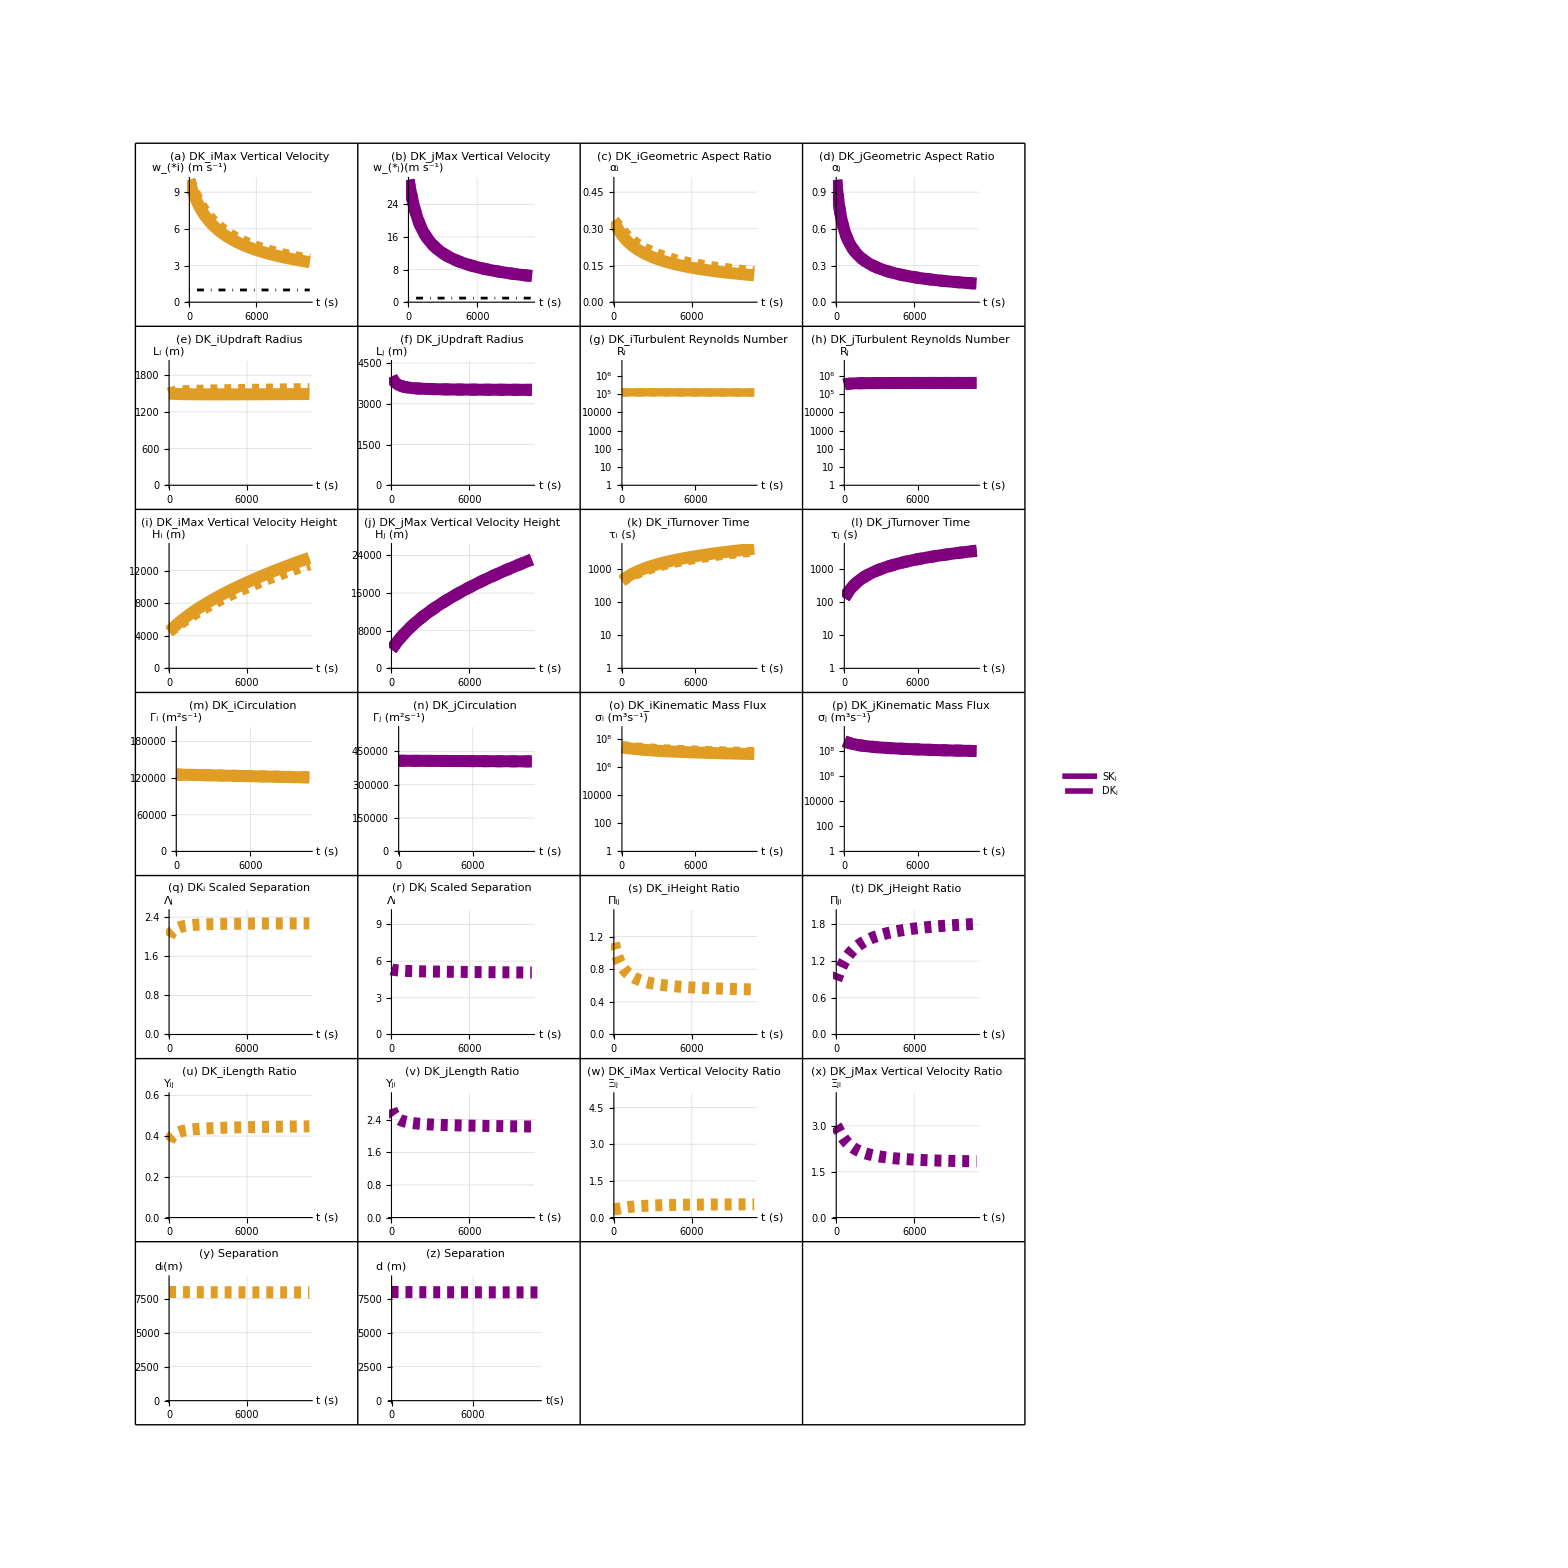
-Graphics-Explicit DK Parameter Evolutions

```mathematica
Labeled[DKImplicitPlotter[LfDK],Text[Style["Explicit DK Parameter Evolutions",FontSize->40]],Top]
```

# Set the KRoNUT trajectories

### Set SK Total Trajectory

```mathematica
SKnTrajectory[T_]:=ParametricPlot[{DαnSKI[t,νnDK,wnDK,LnDK,HnDK],DRnSKI[t,νnDK,wnDK,LnDK,HnDK]},{t,tInitial+.1,T},ScalingFunctions->{"Log10","Log10"},Frame->False,PlotStyle->PlotStyleSKi];
```

```mathematica
SKfTrajectory[T_]:=ParametricPlot[{DαnSKI[t,νnDK,wfDK,LfDK,HfDK],DRnSKI[t,νnDK,wfDK,LfDK,HfDK]},{t,tInitial+.1,T},ScalingFunctions->{"Log10","Log10"},Frame->False,PlotStyle->PlotStyleSKj];
```

### DK Total Trajectory

```mathematica
DKnfTrajectory[T_]:=ParametricPlot[{DαnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0],DRnDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]},{t,tInitial+.1,T},ScalingFunctions->{"Log10","Log10"},Frame->False,PlotStyle->{PlotStyleDKi}];
```

```mathematica
DKfnTrajectory[T_]:=ParametricPlot[{DαnDKI[t,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK],DRnDKI[t,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK]},{t,tInitial+.1,T},ScalingFunctions->{"Log10","Log10"},Frame->False,PlotStyle->PlotStyleDKj]
```

# Generate the specified DK phase portrait

## Near field implicit quantity set

```mathematica
ΛnfSet[t_]=DdDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]/LfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0];
```

```mathematica
ΠnfSet[t_]=HnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]/HfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0];
```

```mathematica
ΞnfSet[t_]=wnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]/wfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0];
```

## Far field implicit quantity set

```mathematica
ΛfnSet[t_]=DdDKI[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]/LnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0];
```

```mathematica
ΠfnSet[t_]=HfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]/HnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0];
```

```mathematica
ΞfnSet[t_]=wfNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0]/wnNumericSolveDK[t,νnDK,wnDK,LnDK,HnDK,xnDK,ynDK,νnDK,wfDK,LfDK,HfDK,dDK[LfDK],0];
```

## Manipulate near field phase portrait

### Colors for the DK

```mathematica
DKiColor=Blue;
```

```mathematica
DKjColor=Magenta;
```

### Manipulate the phase portraits

```mathematica
Manipulate[Legended[GraphicsGrid[{{Show[PhasePlaneDK[ΛnfSet[T],ΠnfSet[T],ΞnfSet[T],i],NullSurfaceSKDαRτPlot[ΛnfSet[T],ΠnfSet[T],ΞnfSet[T],DKiColor],FixedLineαRPlaneSK[DKiColor],FixedLineαRPlaneDK[ΛnfSet[T],ΠnfSet[T],ΞnfSet[T],DKiColor],SKnTrajectory[T],DKnfTrajectory[T]],Show[PhasePlaneDK[ΛfnSet[T],ΠfnSet[T],ΞfnSet[T],j],NullSurfaceSKDαRτPlot[ΛfnSet[T],ΠfnSet[T],ΞfnSet[T],DKjColor],FixedLineαRPlaneSK[DKjColor],FixedLineαRPlaneDK[ΛfnSet[T],ΠfnSet[T],ΞfnSet[T],DKjColor],SKfTrajectory[T],DKfnTrajectory[T]]}}],{FixedLineLegendSK[i,DKiColor],FixedLineLegendDK[i,DKiColor],NullSurfaceLegendDK[i,DKiColor],ImplicitPlotLegendDKi,FixedLineLegendSK[j,DKjColor],FixedLineLegendDK[j,DKjColor],NullSurfaceLegendDK[j,DKjColor],ImplicitPlotLegendDKj}],{T,tInitial,tFinal}];
```

### Generate the phase portraits and label them

```mathematica
PhasePortraitSKi:= Show[PhasePlaneDK[ΛnfSet[tInitial],ΠnfSet[tInitial],ΞnfSet[tInitial],i,tInitial,a],NullSurfaceSKDαRτPlot[ΛnfSet[tInitial],ΠnfSet[tInitial],ΞnfSet[tInitial],DKiColor],FixedLineαRPlaneSK[DKiColor],FixedLineαRPlaneDK[ΛnfSet[tInitial],ΠnfSet[tInitial],ΞnfSet[tInitial],DKiColor],SKnTrajectory[tInitial],DKnfTrajectory[tInitial]]
```

```mathematica
PhasePortraitSKj:=Show[PhasePlaneDK[ΛfnSet[tInitial],ΠfnSet[tInitial],ΞfnSet[tInitial],j,tInitial,b],NullSurfaceSKDαRτPlot[ΛfnSet[tInitial],ΠfnSet[tInitial],ΞfnSet[tInitial],DKjColor],FixedLineαRPlaneSK[DKjColor],FixedLineαRPlaneDK[ΛfnSet[tInitial],ΠfnSet[tInitial],ΞfnSet[tInitial],DKjColor],SKfTrajectory[tInitial],DKfnTrajectory[tInitial]]
```

```mathematica
PhasePortraitDKi:=Show[PhasePlaneDK[ΛnfSet[tFinal],ΠnfSet[tFinal],ΞnfSet[tFinal],i,tFinal,c],NullSurfaceSKDαRτPlot[ΛnfSet[tFinal],ΠnfSet[tFinal],ΞnfSet[tFinal],DKiColor],FixedLineαRPlaneSK[DKiColor],FixedLineαRPlaneDK[ΛnfSet[tFinal],ΠnfSet[tFinal],ΞnfSet[tFinal],DKiColor],SKnTrajectory[tFinal],DKnfTrajectory[tFinal]]
```

```mathematica
PhasePortraitDKj:=Show[PhasePlaneDK[ΛfnSet[tFinal],ΠfnSet[tFinal],ΞfnSet[tFinal],j,tFinal,d],NullSurfaceSKDαRτPlot[ΛfnSet[tFinal],ΠfnSet[tFinal],ΞfnSet[tFinal],DKjColor],FixedLineαRPlaneSK[DKjColor],FixedLineαRPlaneDK[ΛfnSet[tFinal],ΠfnSet[tFinal],ΞfnSet[tFinal],DKjColor],SKfTrajectory[tFinal],DKfnTrajectory[tFinal]]
```

### Generate the DK Implicit Grid Legend

```mathematica
ImplicitLegendDK=Grid[{{FixedLineLegendSK[i,DKiColor]},{FixedLineLegendDK[i,DKiColor]},{NullSurfaceLegendDK[i,DKiColor]},{ImplicitPlotLegendDKi},{FixedLineLegendSK[j,DKjColor]},{FixedLineLegendDK[j,DKjColor]},{NullSurfaceLegendDK[j,DKjColor]},{ImplicitPlotLegendDKj}},Alignment->Left]
```

### Generate the initial and final phase portraits for the DK configuration

```mathematica
Legended[Labeled[GraphicsGrid[{{PhasePortraitSKi,PhasePortraitSKj},{PhasePortraitDKi,PhasePortraitDKj}},Frame->All],Text[Style["Implicit DK Temporal Evolution",FontSize->30]],Top],ImplicitLegendDK]
```

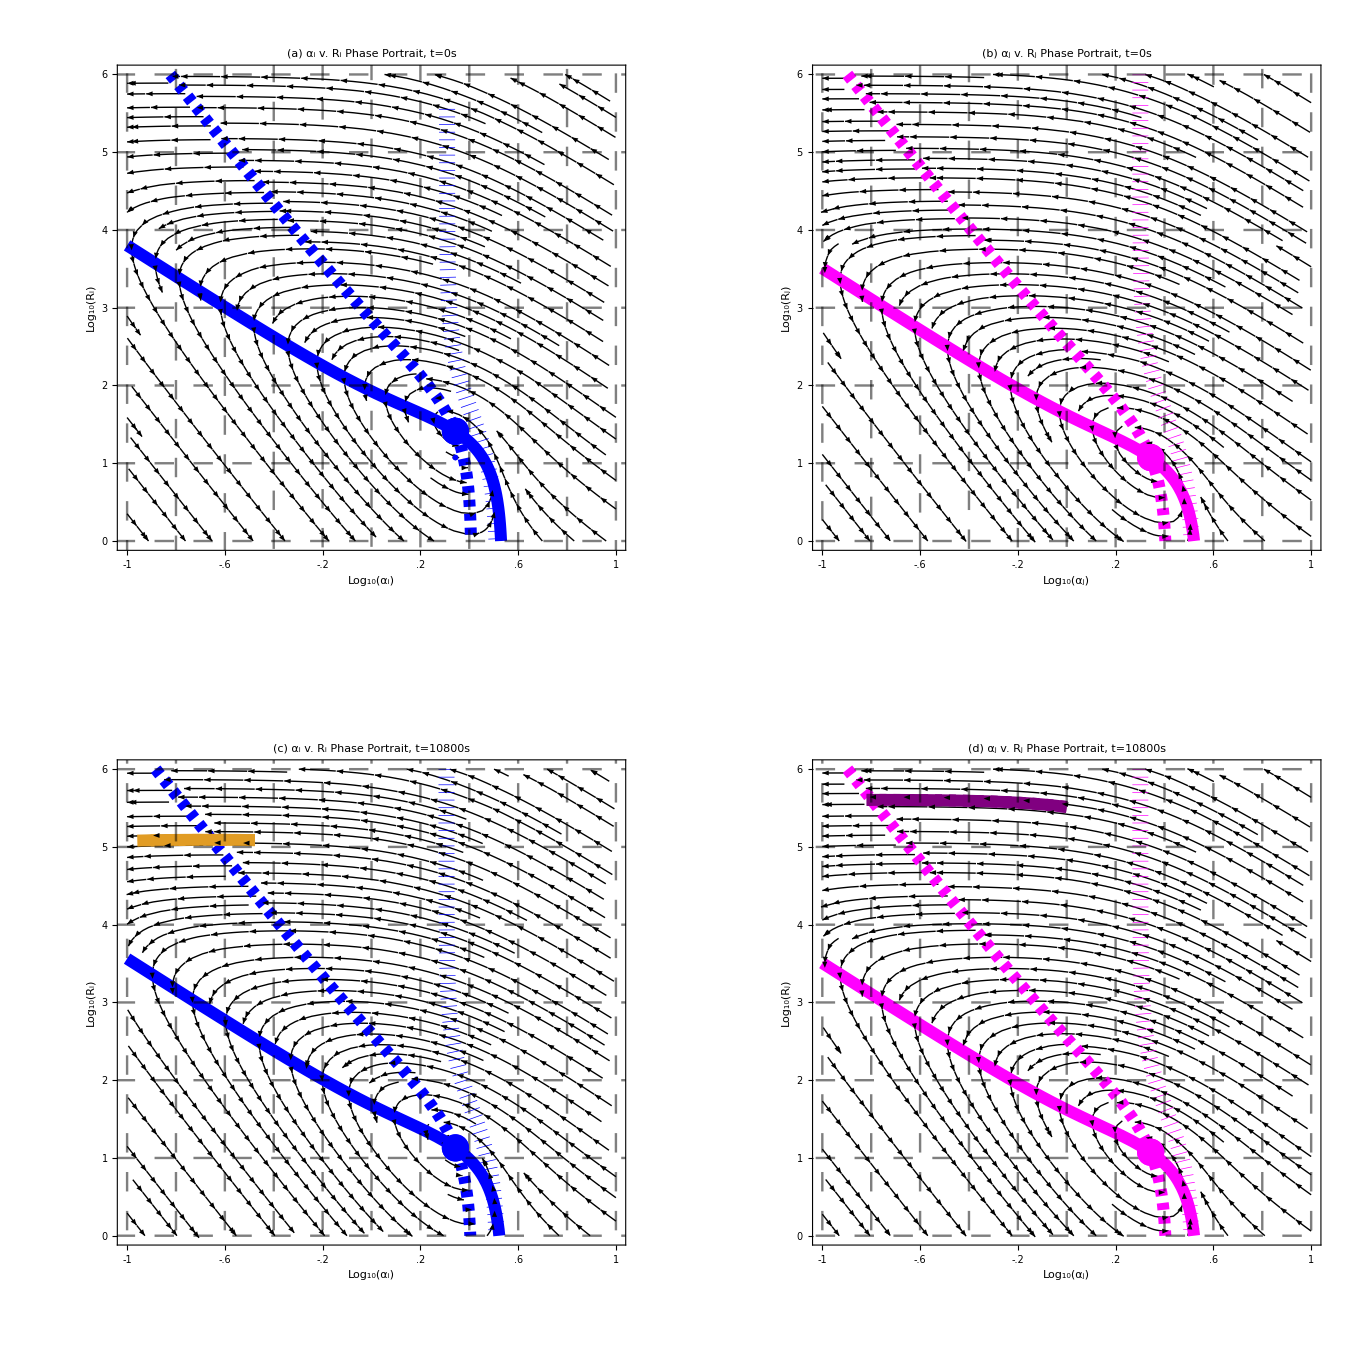
```mathematica
-Graphics-"Implicit DK Temporal Evolution"
```

# #)Saving

```mathematica
DoNUTEvolution[n_]:=Table[{wnNumericSolve[T,νnListSK[[n]],wnListSK[[n]],LnListSK[[n]],HnListSK[[n]]],LnNumericSolve[T,νnListSK[[n]],wnListSK[[n]],LnListSK[[n]],HnListSK[[n]]],HnNumericSolve[T,νnListSK[[n]],wnListSK[[n]],LnListSK[[n]],HnListSK[[n]]]},{T,tInitial,tFinal}];
```

```mathematica
Export["DoNUTEvolution- ν1=1000-w1=1-L1=500-H1=2000.csv",DoNUTEvolution[3]]
```

DoNUTEvolution- ν1=1000-w1=1-L1=500-H1=2000.csv

```mathematica
SystemOpen["DoNUTEvolution4.csv"]
```

```mathematica
TestDoNUTEvolution=Table[Table[{wnNumericSolve[T,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],LnNumericSolve[T,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]],HnNumericSolve[T,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]]},{T,tInitial,tFinal}],{i,1,Length[wnListSK]}];
```

```mathematica
Table[Export["testDoNUTEvolution"<>ToString[i]<>": ν1="<>ToString[νnListSK[[i]]]<>"-w1="<>ToString[wnListSK[[i]]]<>"-L1="<>ToString[LnListSK[[i]]]<>"-H1="<>ToString[HnListSK[[i]]]<>".csv",DoNUTEvolution[[i]]],{i,1,Length[wnListSK]}]
```

{testDoNUTEvolution1: ν1=1000-w1=1-L1=2000-H1=500.csv,testDoNUTEvolution2: ν1=1-w1=3-L1=2000-H1=500.csv,testDoNUTEvolution3: ν1=1000-w1=1-L1=500-H1=2000.csv,testDoNUTEvolution4: ν1=1-w1=3-L1=500-H1=2000.csv}

```mathematica
ClearAll[DoNUTEvolution]
```

## Generating plots of trajectory evolutions in (αn, Rn, τn) phase space

### Compute the implicit quantities associated with the space

```mathematica
αnN[t_,i_]:=αnSK[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]]
```

```mathematica
RnN[t_,i_]:=RnSK[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]]
```

```mathematica
τnN[t_,i_]:=τnSK[t,νnListSK[[i]],wnListSK[[i]],LnListSK[[i]],HnListSK[[i]]]
```

```mathematica
FixedLineN={2.204767957878135,11.845265863140161};
```

```mathematica
ListLinePlot3D[Table[{FixedLineN[[1]],FixedLineN[[2]],t},{t,0,10,1}]]
```

-Graphics3D-

```mathematica
testPlot[T_,step_,i_]:=ListLinePlot3D[{Table[{αnN[t,i],RnN[t,i],τnN[t,i]},{t,0,T,step}],Table[{FixedLineN[[1]],FixedLineN[[2]],t},{t,0,T,step}]},PlotRange->All]
```

```mathematica
testPlot[tFinal,1,3]
```

InterpolatingFunction::dmval: Input value {2701} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

## Sh. test SK set

## Sh. test cases

```mathematica
νnListSK={1,1,1000,1000,2*114.74};
```

```mathematica
wnListSK={3,3,1,1,2};
```

```mathematica
LnListSK={2000,500,500,2000,1102.38};
```

```mathematica
HnListSK={500,2000,2000,500,500};
```

## Ranges for explicit plot

### wn plot range

```mathematica
wPlotMinSK=0;
```

```mathematica
wPlotMaxSK=6.5;
```

### Ln plot range

```mathematica
LPlotMinSK=0;
```

```mathematica
LPlotMaxSK=11000;
```

### Hn plot range

```mathematica
HPlotMinSK=0;
```

```mathematica
HPlotMaxSK=5500;
```

### αn plot range

```mathematica
αPlotMinSK=0;
```

```mathematica
αPlotMaxSK=4.2;
```

### Rn plot range

```mathematica
RPlotMinSK=.001;
```

```mathematica
RPlotMaxSK=10^6;
```

### τn plot range

```mathematica
τPlotMinSK=1;
```

```mathematica
τPlotMaxSK=5*10^7;
```

### Γn plot range

```mathematica
ΓPlotMinSK=0;
```

```mathematica
ΓPlotMaxSK=55000;
```

### σn plot range

```mathematica
σPlotMinSK=1;
```

```mathematica
σPlotMaxSK=10^11;
```

# Md. test SK set

## Md. test cases

```mathematica
νnListSK={1,1,1000,1000};
```

```mathematica
wnListSK={10,10,3,3};
```

```mathematica
LnListSK={4500,1500,1500,4500};
```

```mathematica
HnListSK={1500,4500,4500,1500};
```

## Ranges for explicit plot

## Ranges for explicit plot

### wn plot range

```mathematica
wPlotMinSK=0;
```

```mathematica
wPlotMaxSK=16.5;
```

### Ln plot range

```mathematica
LPlotMinSK=0;
```

```mathematica
LPlotMaxSK=10500;
```

### Hn plot range

```mathematica
HPlotMinSK=0;
```

```mathematica
HPlotMaxSK=18000;
```

### αn plot range

```mathematica
αPlotMinSK=0;
```

```mathematica
αPlotMaxSK=3.2;
```

### Rn plot range

```mathematica
RPlotMinSK=.001;
```

```mathematica
RPlotMaxSK=10^6;
```

### τn plot range

```mathematica
τPlotMinSK=1;
```

```mathematica
τPlotMaxSK=5*10^6;
```

### Γn plot range

```mathematica
ΓPlotMinSK=0;
```

```mathematica
ΓPlotMaxSK=150000;
```

### σn plot range

```mathematica
σPlotMinSK=1;
```

```mathematica
σPlotMaxSK=10^11;
```

# Dp. test SK set

## Dp. test cases

```mathematica
νnListSK={1,1,1000,1000};
```

```mathematica
wnListSK={30,30,5,5};
```

```mathematica
LnListSK={8000,4000,4000,8000};
```

```mathematica
HnListSK={4000,8000,8000,4000};
```

## Ranges for explicit plot

### wn plot range

```mathematica
wPlotMinSK=0;
```

```mathematica
wPlotMaxSK=34;
```

### Ln plot range

```mathematica
LPlotMinSK=0;
```

```mathematica
LPlotMaxSK=11000;
```

### Hn plot range

```mathematica
HPlotMinSK=0;
```

```mathematica
HPlotMaxSK=34000;
```

### αn plot range

```mathematica
αPlotMinSK=0;
```

```mathematica
αPlotMaxSK=2.2;
```

### Rn plot range

```mathematica
RPlotMinSK=1;
```

```mathematica
RPlotMaxSK=5*10^6;
```

### τn plot range

```mathematica
τPlotMinSK=1;
```

```mathematica
τPlotMaxSK=5*10^5;
```

### Γn plot range

```mathematica
ΓPlotMinSK=0;
```

```mathematica
ΓPlotMaxSK=9*10^5;
```

### σn plot range

```mathematica
σPlotMinSK=1;
```

```mathematica
σPlotMaxSK=10^11;
```

# DK Test Case 1 Implicit Plot Ranges

## Near field implicit plot range

### wn plot range

```mathematica
wnPlotMinDK=0;
```

```mathematica
wnPlotMaxDK=8;
```

### Ln plot range

```mathematica
LnPlotMinDK=0;
```

```mathematica
LnPlotMaxDK=10000;
```

### Hn plot range

```mathematica
HnPlotMinDK=0;
```

```mathematica
HnPlotMaxDK=8000;
```

### αn plot range

```mathematica
αnPlotMinDK=0;
```

```mathematica
αnPlotMaxDK=4;
```

### Rn plot range

```mathematica
RnPlotMinDK=0;
```

```mathematica
RnPlotMaxDK=100;
```

### τn plot range

```mathematica
τnPlotMinDK=0;
```

```mathematica
τnPlotMaxDK=5000;
```

### Γn plot range

```mathematica
ΓnPlotMinDK=0;
```

```mathematica
ΓnPlotMaxDK=100000;
```

### σn plot range

```mathematica
σnPlotMinDK=0;
```

```mathematica
σnPlotMaxDK=5*10^8;
```

### dnf plot range

```mathematica
dnfPlotMinDK=0;
```

```mathematica
dnfPlotMaxDK=5000;
```

### Λnf plot range

```mathematica
ΛnfPlotMinDK=0;
```

```mathematica
ΛnfPlotMaxDK=2;
```

### Πnf plot range

```mathematica
ΠnfPlotMinDK=0;
```

```mathematica
ΠnfPlotMaxDK=2;
```

### Υnf plot range

```mathematica
ΥnfPlotMinDK=0;
```

```mathematica
ΥnfPlotMaxDK=3;
```

### Ξnf plot range

```mathematica
ΞnfPlotMinDK=0;
```

```mathematica
ΞnfPlotMaxDK=60;
```

## Far field implicit plot range

### wf plot range

```mathematica
wfPlotMinDK=0;
```

```mathematica
wfPlotMaxDK=8;
```

### Ln plot range

```mathematica
LfPlotMinDK=0;
```

```mathematica
LfPlotMaxDK=10000;
```

### Hn plot range

```mathematica
HfPlotMinDK=0;
```

```mathematica
HfPlotMaxDK=8000;
```

### αn plot range

```mathematica
αfPlotMinDK=0;
```

```mathematica
αfPlotMaxDK=4;
```

### Rf plot range

```mathematica
RfPlotMinDK=0;
```

```mathematica
RfPlotMaxDK=30;
```

### τf plot range

```mathematica
τfPlotMinDK=0;
```

```mathematica
τfPlotMaxDK=500000;
```

### Γf plot range

```mathematica
ΓfPlotMinDK=0;
```

```mathematica
ΓfPlotMaxDK=60000;
```

### σf plot range

```mathematica
σfPlotMinDK=0;
```

```mathematica
σfPlotMaxDK=10^8;
```

### dfn plot range

```mathematica
dfnPlotMinDK=0;
```

```mathematica
dfnPlotMaxDK=5000;
```

### Λfn plot range

```mathematica
ΛfnPlotMinDK=0;
```

```mathematica
ΛfnPlotMaxDK=2;
```

### Πfn plot range

```mathematica
ΠfnPlotMinDK=0;
```

```mathematica
ΠfnPlotMaxDK=2;
```

### Υfn plot range

```mathematica
ΥfnPlotMinDK=0;
```

```mathematica
ΥfnPlotMaxDK=3;
```

### Ξfn plot range

```mathematica
ΞfnPlotMinDK=0;
```

```mathematica
ΞfnPlotMaxDK=4;
```

# DK Test Case 2 Implicit Plot Ranges

## Near field implicit plot range

### wn plot range

```mathematica
wnPlotMinDK=0;
```

```mathematica
wnPlotMaxDK=10;
```

### Ln plot range

```mathematica
LnPlotMinDK=0;
```

```mathematica
LnPlotMaxDK=2000;
```

### Hn plot range

```mathematica
HnPlotMinDK=0;
```

```mathematica
HnPlotMaxDK=15000;
```

### αn plot range

```mathematica
αnPlotMinDK=0;
```

```mathematica
αnPlotMaxDK=.5;
```

### Rn plot range

```mathematica
RnPlotMinDK=1;
```

```mathematica
RnPlotMaxDK=5*10^6;
```

### τn plot range

```mathematica
τnPlotMinDK=1;
```

```mathematica
τnPlotMaxDK=5000;
```

### Γn plot range

```mathematica
ΓnPlotMinDK=0;
```

```mathematica
ΓnPlotMaxDK=200000;
```

### σn plot range

```mathematica
σnPlotMinDK=1;
```

```mathematica
σnPlotMaxDK=5*10^8;
```

### dnf plot range

```mathematica
dnfPlotMinDK=0;
```

```mathematica
dnfPlotMaxDK=9000;
```

### Λnf plot range

```mathematica
ΛnfPlotMinDK=0;
```

```mathematica
ΛnfPlotMaxDK=2.5;
```

### Πnf plot range

```mathematica
ΠnfPlotMinDK=0;
```

```mathematica
ΠnfPlotMaxDK=1.5;
```

### Υnf plot range

```mathematica
ΥnfPlotMinDK=0;
```

```mathematica
ΥnfPlotMaxDK=.6;
```

### Ξnf plot range

```mathematica
ΞnfPlotMinDK=0;
```

```mathematica
ΞnfPlotMaxDK=5;
```

## Far field implicit plot range

### wf plot range

```mathematica
wfPlotMinDK=0;
```

```mathematica
wfPlotMaxDK=30;
```

### Lf plot range

```mathematica
LfPlotMinDK=0;
```

```mathematica
LfPlotMaxDK=4500;
```

### Hf plot range

```mathematica
HfPlotMinDK=0;
```

```mathematica
HfPlotMaxDK=26000;
```

### αf plot range

```mathematica
αfPlotMinDK=0;
```

```mathematica
αfPlotMaxDK=1;
```

### Rf plot range

```mathematica
RfPlotMinDK=1;
```

```mathematica
RfPlotMaxDK=5*10^6;
```

### τf plot range

```mathematica
τfPlotMinDK=1;
```

```mathematica
τfPlotMaxDK=5000;
```

### Γf plot range

```mathematica
ΓfPlotMinDK=0;
```

```mathematica
ΓfPlotMaxDK=5.5*10^5;
```

### σf plot range

```mathematica
σfPlotMinDK=1;
```

```mathematica
σfPlotMaxDK=5*10^9;
```

### dfn plot range

```mathematica
dfnPlotMinDK=0;
```

```mathematica
dfnPlotMaxDK=9000;
```

### Λfn plot range

```mathematica
ΛfnPlotMinDK=0;
```

```mathematica
ΛfnPlotMaxDK=10;
```

### Πfn plot range

```mathematica
ΠfnPlotMinDK=0;
```

```mathematica
ΠfnPlotMaxDK=2;
```

### Υfn plot range

```mathematica
ΥfnPlotMinDK=0;
```

```mathematica
ΥfnPlotMaxDK=3;
```

### Ξfn plot range

```mathematica
ΞfnPlotMinDK=0;
```

```mathematica
ΞfnPlotMaxDK=4;
```